```mathematica
Du=D[r^2 D[u[r],r],r]+((λ r^2)/v[r]^2-(l(l+1)-(r^2(ω+4π G))/v[r]^2)u[r]);
```

```mathematica
v[r_]:=a^2-b^2 r^2
```

```mathematica
b=0;
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,FullSimplify[Simplify[ExpandAll[Simplify[DSolve[Du==0,u[r],r]]]]]]
```

{{u[r]→1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(C[1]+2^(-2+l) a^(-4+2 l) l √π r^2 λ (-ⅈ r √(-4 G π-ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,-(ⅈ r √(-4 G π-ω))/a^2]+C[2] SphericalBesselY[l,-(ⅈ r √(-4 G π-ω))/a^2]}}

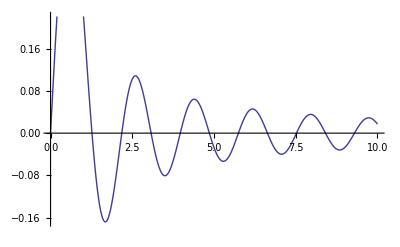

```mathematica
a=1;
λ=0;
l=1;
G=1;
ω=0;
A=1;
B=0;
Plot[{Re[1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]],},{r,0,10}]
```

```mathematica
1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]
```